```mathematica
m=1; m2=1;λ=1; g=1.1; c=0.6; λ2=0; ϵ=0.02;  
kr= √((m/2)^2-m2^2) //N
krs=√((2m)^2-m^2)//N
ωe=m √(1-ϵ^2);
H=0;
Γ=0;
Γd=c^2/(2 m^3)If[m>2 m2,1/√(1-((2 m2)/m)^2),0];1/Γd;
```

0.+0.866025 ⅈ

1.73205

Power::infy: Infinite expression 1/0 encountered.

```mathematica
(*kw=m;*)
tend=1000;

ω[k_]:=√(k^2+m2^2);
χi[k_]:=(ω[k]/π)^(-1/2)
χid[k_]:=I ω[k]χi[k]
```

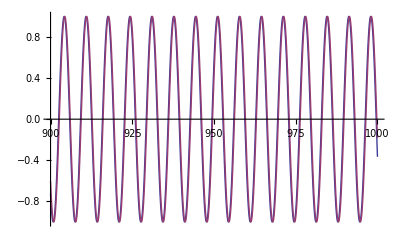

```mathematica
ΦH=1;
Φpump=First[NDSolve[{y''[tx]+m^2 y[tx]-λ/(3!)y[tx]^3+g/(5!)y[tx]^5==0,y[0]==ΦH,y'[0]==0},y,{tx,0,tend}]];
A=√((2 m^2)/λ);
B=(g/12+λ^2/(96 m^2))A^5/(2 m^2);
ωp[ϵp_]:=m √(1-ϵp^2)
ys[t_,ϵp_]:=2 ϵp A Cos[t ωp[ϵp]]+ 2  ϵp^3((-λ A^3)/(48 m^2)Cos[3 t ωp[ϵp]]+B Cos[t ωp[ϵp]])
ϵ=ϵp/.FindRoot[ys[0,ϵp]==ΦH,{ϵp,0.3,0,1}];
Plot[{y[t]/.Φpump,ys[t,ϵ]},{t,tend-100,tend}]
```

```mathematica
xo=m^-1 ϵ^-1; xo=m^-1 0.02^-1;
f[k_]:=π xo Sech[k(π xo)/2]

xw=1000;
L=2 xw;
ΦO=(*ΦH √((m L ϵ)/2); *) 4 ϵ √(m^2/λ); ΦO=1.2;
u[t_,x_,ω_]:=4 ArcTan[(√(1-ω^2)Cos[ω t])/(ω Cosh[√(1-ω^2)x])]

ϕpH[t_]:= (*ΦH Sin[ωp t]*)(* u[t,0,ωp]*)(*y[t]/.Φpump*) ys[t,ϵ]
ϕpO[t_]:= ΦO Sin[ωp[ϵ] t]

sm[k_]:=If[k==0,1,1/2 k π xo Csch[k (π xo)/2]]
fp[t_,k_]:=2xo(-λ/2 ϕpO[t]^2+g/(4!)ϕpO[t]^4 1/6(4+k^2 xo^2))sm[k]
fpH[t_]:=-λ/2 ϕpH[t]^2+g/(4!)ϕpH[t]^4

EH=L/2 m^2 ΦH^2; NH=EH/m;
EO=m/ϵ ΦO^2;
```

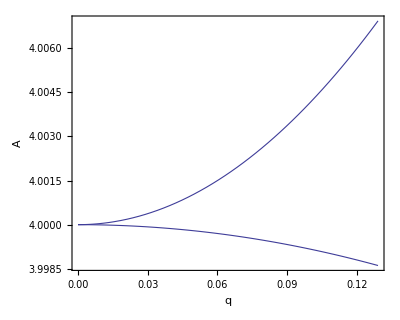

1.66069

1.65849

```mathematica
(* --- Mathieu instability chart -----*)
Av[k_]:=(*4 ω[k]^2/m^2;*)(ω[k]^2-λ ΦH^2/4+g ΦH^4/64)/ωp[ϵ]^2

qv=(*(4 c ΦH)/m^2;*)(λ ΦH^2/8-g ΦH^4/96)/ωp[ϵ]^2;
pv=(g ΦH^4/384)/ωp[ϵ]^2;
Plot[{Table[{MathieuCharacteristicA[r,q],MathieuCharacteristicB[r,q]},{r,2,2}]},{q,0,qv},Frame->True,AspectRatio->0.8,PlotStyle->Thickness[0.002],FrameLabel->{"q","A"},FrameStyle->18,Axes->False]
kA=N[-k/.First[First[Solve[Av[k]==MathieuCharacteristicA[2,qv],k]]]]
kB=N[-k/.First[First[Solve[Av[k]==MathieuCharacteristicB[2,qv],k]]]]
```

```mathematica
nmin=500; nmax=550;
Nv=nmax-nmin+1;
kv=N[Table[(2 π n)/L,{n,nmin,nmax}]]
kvmn=kv[[1]];  
kvmx=kv[[Nv]];
```

{1.5708,1.57394,1.57708,1.58022,1.58336,1.5865,1.58965,1.59279,1.59593,1.59907,1.60221,1.60535,1.6085,1.61164,1.61478,1.61792,1.62106,1.6242,1.62734,1.63049,1.63363,1.63677,1.63991,1.64305,1.64619,1.64934,1.65248,1.65562,1.65876,1.6619,1.66504,1.66819,1.67133,1.67447,1.67761,1.68075,1.68389,1.68704,1.69018,1.69332,1.69646,1.6996,1.70274,1.70588,1.70903,1.71217,1.71531,1.71845,1.72159,1.72473,1.72788}

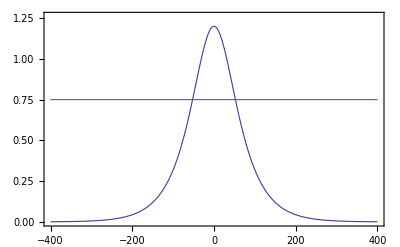

```mathematica
Plot[{ΦO Sech[x/xo],ΦH},{x,-xw,xw},PlotRange->{0,1.05ΦO},Frame->True,PlotStyle->Thickness[0.002],Axes->False]
```

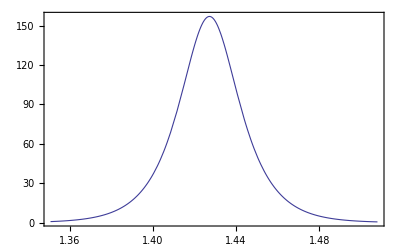

```mathematica
Plot[{f[k-(kA+kB)/2]},{k,kvmn,kvmx},PlotRange->All,Frame->True,Axes->False,PlotStyle->Thickness[0.002]]
```

```mathematica
ϕv=First[ NDSolve[{D[χ[t,k],t,t]+(ω[k]^2+ fpH[t](*2 c ϕpH[t]*))χ[t,k]==0,χ[0,k]==χi[k],Derivative[1,0][χ][0,k]==χid[k]},χ,{t,0,tend},{k,kvmn,kvmx},MaxStepFraction->1/800,PrecisionGoal->4]];
```

```mathematica
eqnsA=Table[{Subscript[χ, j]''[t]+(ω[kv[[j]]]^2+fpH[t])Subscript[χ, j][t]==0,Subscript[χ, j][0]==χi[kv[[j]]],Subscript[χ, j]'[0]==χid[kv[[j]]]},{j,1,Nv}];
varsA=Table[Subscript[χ, j],{j,1,Nv}];
ϕvA=First[NDSolve[eqnsA,varsA,{t,0,tend},Method->{"ExplicitRungeKutta", "DifferenceOrder"->8}, InterpolationOrder->All]];
```

```mathematica
(*eqns=Table[{Subscript[χ, j]''[t]+ω[kv[[j]]]^2 Subscript[χ, j][t]+ 2 c ϕpO[t]Sum[1/L f[kv[[j]]-kv[[jp]]]Subscript[χ, jp][t],{jp,1,Nv}]==0,Subscript[χ, j][0]==χi[kv[[j]]],Subscript[χ, j]'[0]==χid[kv[[j]]]},{j,1,Nv}];
vars=Table[Subscript[χ, j],{j,1,Nv}];
ϕvS=First[NDSolve[eqns,vars,{t,0,tend},Method->{"ExplicitRungeKutta", "DifferenceOrder"->8}, InterpolationOrder->All]];*)
```

```mathematica
eqns2=Table[{Subscript[χ, j]''[t]+ω[kv[[j]]]^2 Subscript[χ, j][t]+Sum[1/L fp[t,kv[[j]]-kv[[jp]]]Subscript[χ, jp][t],{jp,1,Nv}]==0,Subscript[χ, j][0]==χi[kv[[j]]],Subscript[χ, j]'[0]==χid[kv[[j]]]},{j,1,Nv}];
vars2=Table[Subscript[χ, j],{j,1,Nv}];
ϕvS2=First[NDSolve[eqns2,vars2,{t,0,tend}(*,Method->{"ExplicitRungeKutta", "DifferenceOrder"->8}, InterpolationOrder->All*)]];
```

```mathematica
(*eqnsF=Table[{Subscript[χ, q,j]''[t]+ω[kv[[j]]]^2 Subscript[χ, q,j][t]+2 c ϕpO[t]Sum[1/L f[kv[[j]]-kv[[jp]]]Subscript[χ, q,jp][t],{jp,1,Nv}]==0,Subscript[χ, q,j][0]==If[q==j,L/(2 π)χi[kv[[j]]],0],Subscript[χ, q,j]'[0]==If[q==j,L/(2 π)χid[kv[[j]]],0]},{j,1,Nv},{q,1,Nv}];
varsF=Table[Subscript[χ, q,j],{j,1,Nv},{q,1,Nv}];
ϕvSF=Table[First[NDSolve[eqnsF[[All,q]],varsF[[All,q]],{t,0,tend}]],{q,1,Nv}];*)
```

```mathematica
eqnsF2=Table[{Subscript[χ, q,j]''[t]+ω[kv[[j]]]^2 Subscript[χ, q,j][t]+Sum[1/L fp[t,kv[[j]]-kv[[jp]]]Subscript[χ, q,jp][t],{jp,1,Nv}]==0,Subscript[χ, q,j][0]==If[q==j,L/(2 π)χi[kv[[j]]],0],Subscript[χ, q,j]'[0]==If[q==j,L/(2 π)χid[kv[[j]]],0]},{j,1,Nv},{q,1,Nv}];
varsF2=Table[Subscript[χ, q,j],{j,1,Nv},{q,1,Nv}];
ϕvSF2=Table[Print[q];
First[NDSolve[eqnsF2[[All,q]],varsF2[[All,q]],{t,0,tend}(*,Method->{"ExplicitRungeKutta", "DifferenceOrder"->8}, InterpolationOrder->All*)]],{q,1,Nv}];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

```mathematica
Animate[ListPlot[{Table[{kv[[j]],(1/(2 π)(1/2 Abs[Derivative[1][Subscript[χ, j]][t]]^2+1/2(kv[[j]]^2+m2^2)Abs[Subscript[χ, j][t]]^2)/.ϕvA)-1/2 √(kv[[j]]^2+m2^2)},{j,1,Nv}](*,Table[{kv[[j]],(1/(2 π)Sum[((2π)/L)^2(1/2 Abs[Derivative[1][Subscript[χ, q,j]][t]]^2+1/2(kv[[j]]^2+m2^2)Abs[Subscript[χ, q,j][t]]^2)/.ϕvSF2[[q]],{q,1,Nv}])-1/2 √(kv[[j]]^2+m2^2)},{j,1,Nv}],Table[{kv[[j]],(1/(2 π)(1/2 Abs[Derivative[1,0][χ][t,kv[[j]]]]^2+1/2(kv[[j]]^2+m2^2)Abs[χ[t,kv[[j]]]]^2)/.ϕv)-1/2 √(kv[[j]]^2+m2^2)},{j,1,Nv}],Table[{kv[[j]],(1/(2 π)(1/2 Abs[Derivative[1][Subscript[χ, j]][t]]^2+1/2(kv[[j]]^2+m2^2)Abs[Subscript[χ, j][t]]^2)/.ϕvS2)-1/2 √(kv[[j]]^2+m2^2)},{j,1,Nv}],Table[{kv[[j]],10^8(kv[[j]]-kA)},{j,1,Nv}],Table[{kv[[j]],10^8(kv[[j]]-kB)},{j,1,Nv}]*)},PlotRange->{{kvmn,kvmx},{-0.01,0.4}},PlotStyle->Thickness[0.0015],AspectRatio->0.4,ImageSize->1000,Joined->True,PlotMarkers->Automatic,Frame->True,Axes->False,FrameLabel->{"Wavenumber k","Energy density E_k",Round[t]},FrameStyle->18],{t,0,tend},AnimationRate->5]
```

```mathematica
tv=0;Table[{kv[[j]],1/(2 π)Sum[((2π)/L)^2(1/2 Abs[Derivative[1][Subscript[χ, q,j]][tv]]^2+1/2(kv[[j]]^2+m2^2)Abs[Subscript[χ, q,j][tv]]^2)/.ϕvSF2[[q]],{q,1,Nv}]},{j,1,Nv}]
```

{{1.53153,0.914545},{1.53938,0.917836},{1.54723,0.921132},{1.55509,0.924432},{1.56294,0.927738},{1.5708,0.931048},{1.57865,0.934363},{1.5865,0.937683},{1.59436,0.941007},{1.60221,0.944336},{1.61007,0.94767},{1.61792,0.951008},{1.62577,0.954351},{1.63363,0.957698},{1.64148,0.961049},{1.64934,0.964405},{1.65719,0.967765},{1.66504,0.97113},{1.6729,0.974498},{1.68075,0.977871},{1.68861,0.981248},{1.69646,0.984629},{1.70431,0.988014},{1.71217,0.991403},{1.72002,0.994796},{1.72788,0.998193},{1.73573,1.00159},{1.74358,1.005},{1.75144,1.00841},{1.75929,1.01182},{1.76715,1.01523},{1.775,1.01865},{1.78285,1.02208},{1.79071,1.0255},{1.79856,1.02893},{1.80642,1.03237},{1.81427,1.03581},{1.82212,1.03925},{1.82998,1.04269},{1.83783,1.04614},{1.84569,1.04959}}

```mathematica
Mpr[t_,k_]:=If[kA> k>kB,EH Γd t,0]
```

```mathematica
zi=π/4;
```

```mathematica
χex[t_,k_]:=(√π √(1/ω[k]) ((-2 ⅈ ω[k] MathieuC[Av[k],qv,zi]+m MathieuCPrime[Av[k],qv,zi]) MathieuS[Av[k],qv,m/2 t+zi]+MathieuC[Av[k],qv,m/2 t+zi] (2 ⅈ ω[k] MathieuS[Av[k],qv,zi]-m MathieuSPrime[Av[k],qv,zi])))/(m (MathieuCPrime[Av[k],qv,zi] MathieuS[Av[k],qv,zi]-MathieuC[Av[k],qv,zi] MathieuSPrime[Av[k],qv,zi]))
```

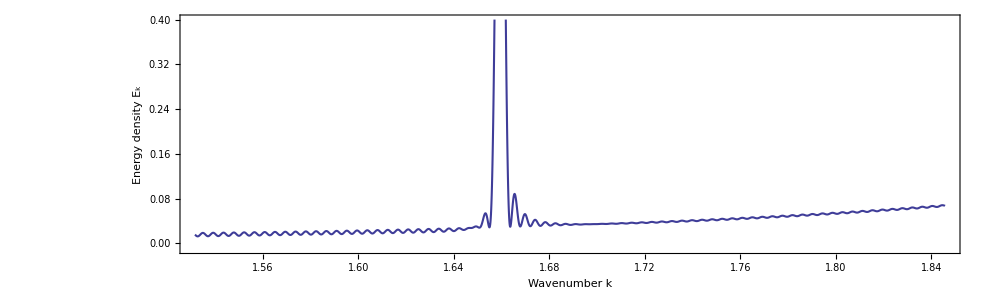

```mathematica
tv=831; 
Plot[{1/(2 π)(1/2 Abs[Derivative[1,0][χ][tv,k]]^2+1/2 ω[k]^2 Abs[χ[tv,k]]^2)-1/2 ω[k]/.ϕv(*,
1/(2 π)(1/2 Abs[Derivative[1,0][χex][tv,k]]^2+1/2 ω[k]^2 Abs[χex[tv,k]]^2)-1/2 ω[k]*)(*,10^8(k-kA),10^8(k-kB)*)},{k,kvmn,kvmx},PlotRange->{{kvmn,kvmx},{-0.01,0.4}},PlotStyle->Thickness[0.0015],AspectRatio->0.3,ImageSize->1000,Frame->True,FrameLabel->{"Wavenumber k","Energy density E_k",Round[tv]},FrameStyle->18,Axes->False]
```

```mathematica
Animate[Plot[{1/(2 π)(1/2 Abs[Derivative[1,0][χ][t,k]]^2+1/2 ω[k]^2 Abs[χ[t,k]]^2)-1/2 ω[k]/.ϕv(*,
1/(2 π)(1/2 Abs[Derivative[1,0][χex][t,k]]^2+1/2 ω[k]^2 Abs[χex[t,k]]^2)-1/2 ω[k]*)(*,10^8(k-kA),10^8(k-kB)*)},{k,kvmn,kvmx},PlotRange->{{kvmn,kvmx},{-0.01,0.4}},PlotStyle->Thickness[0.0015],AspectRatio->0.3,ImageSize->1000,Frame->True,FrameLabel->{"Wavenumber k","Energy density E_k",Round[t]},FrameStyle->18,Axes->False],{t,0,tend},AnimationRate->10]
```

```mathematica
tvmin=10; tvmax=300; tvstep=10;
```

```mathematica
dtab=Table[{tv,NIntegrate[L/(2 π)(1/(2 π)(1/2 Abs[Derivative[1,0][χ][tv,k]]^2+1/2(k^2+m2^2)Abs[χ[tv,k]]^2)-1/2 √(k^2+m2^2))/.ϕv,{k,0.3,0.5},AccuracyGoal->3]},{tv,tvmin,tvmax,tvstep}];
```

```mathematica
dtabex=Table[{tv,NIntegrate[L/(2 π)(1/(2 π)(1/2 Abs[Derivative[1,0][χex][tv,k]]^2+1/2(k^2+m2^2)Abs[χex[tv,k]]^2)-1/2 √(k^2+m2^2)),{k,0.3,0.5},AccuracyGoal->3]},{tv,tvmin,tvmax,tvstep}];
```

```mathematica
dtabp=Table[{tv,EH Γd tv},{tv,tvmin,tvmax,tvstep}];
```

```mathematica
dtabp2=Table[{tv,EH(E^(Γd tv)-1)},{tv,tvmin,tvmax,tvstep}];
```

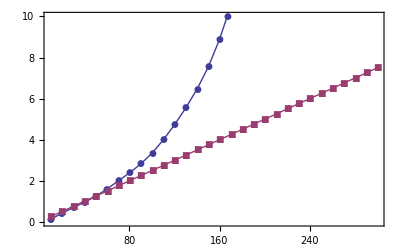

```mathematica
ListPlot[{dtabex,dtabp},Joined->True,ImageSize->400,Frame->True,FrameStyle->15,Axes->False,PlotMarkers->Automatic,PlotRange->{0,10}]
```

```mathematica
Simplify[DSolve[{y''[z]+(Ak-2 qk Cos[2 z])y[z]==0,y[0]==√(π/ωk),y'[0]==2/mo I ωk √(π/ωk)},y[z],z]]
```

{{y[z]→(√π √(1/ωk) ((-2 ⅈ ωk MathieuC[Ak,qk,0]+mo MathieuCPrime[Ak,qk,0]) MathieuS[Ak,qk,z]+MathieuC[Ak,qk,z] (2 ⅈ ωk MathieuS[Ak,qk,0]-mo MathieuSPrime[Ak,qk,0])))/(mo (MathieuCPrime[Ak,qk,0] MathieuS[Ak,qk,0]-MathieuC[Ak,qk,0] MathieuSPrime[Ak,qk,0]))}}

```mathematica
Simplify[DSolve[{y''[z]+(Ak-2 qk Cos[2 z])y[z]==0,y[π/2]==√(π/ωk),y'[π/2]==2/mo I ωk √(π/ωk)},y[z],z]]
```

{{y[z]→(√π √(1/ωk) ((-2 ⅈ ωk MathieuC[Ak,qk,π/2]+mo MathieuCPrime[Ak,qk,π/2]) MathieuS[Ak,qk,z]+MathieuC[Ak,qk,z] (2 ⅈ ωk MathieuS[Ak,qk,π/2]-mo MathieuSPrime[Ak,qk,π/2])))/(mo (MathieuCPrime[Ak,qk,π/2] MathieuS[Ak,qk,π/2]-MathieuC[Ak,qk,π/2] MathieuSPrime[Ak,qk,π/2]))}}